```mathematica
f[n_,i_]:=(1 - Exp[(-2 n)/(i-1)a (g-x)])PDF[NormalDistribution[0,√((i-1)/n)],x](g-x)PDF[NormalDistribution[0,1/(√n)],x - g]
```

```mathematica
g[n_,i_]:=(1 - Exp[-2(1-n/(i+1))a (g-x)])PDF[NormalDistribution[0,√(1-(i+1)/n)],x](g-x)PDF[NormalDistribution[0,1/(√n)],x - g]
```

```mathematica
xlist =Table[NIntegrate[f[n,6]/. g-> 1 /.a -> 1,{x,-∞,1}],{n,1,100}]
```

{0.0249742,0.0324949,0.0366159,0.0388999,0.040014,0.0403285,0.0400769,0.0394184,0.0384666,0.0373054,0.0359978,0.0345923,0.033126,0.0316279,0.0301204,0.0286209,0.027143,0.0256967,0.02429,0.0229284,0.0216161,0.0203558,0.0191491,0.017997,0.0168995,0.0158562,0.0148663,0.0139286,0.0130418,0.0122042,0.011414,0.0106694,0.00996851,0.0093094,0.0086901,0.0081087,0.00756327,0.00705195,0.00657292,0.00612442,0.00570474,0.00531223,0.00494533,0.00460253,0.00428238,0.00398352,0.00370463,0.0034445,0.00320193,0.00297583,0.00276514,0.00256887,0.00238609,0.00221592,0.00205754,0.00191016,0.00177305,0.00164554,0.00152696,0.00141673,0.00131427,0.00121906,0.0011306,0.00104842,0.000972101,0.00090123,0.000835429,0.000774347,0.000717653,0.00066504,0.000616221,0.00057093,0.000528916,0.000489948,0.000453809,0.000420299,0.000389229,0.000360426,0.000333727,0.000308981,0.000286047,0.000264796,0.000245105,0.000226862,0.000209962,0.000194307,0.000179808,0.000166379,0.000153943,0.000142428,0.000131766,0.000121895,0.000112757,0.000104297,0.0000964673,0.0000892202,0.0000825129,0.0000763059,0.0000705621,0.0000652473}

```mathematica
ylist = Table[1/n,{n,1,100}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22,1/23,1/24,1/25,1/26,1/27,1/28,1/29,1/30,1/31,1/32,1/33,1/34,1/35,1/36,1/37,1/38,1/39,1/40,1/41,1/42,1/43,1/44,1/45,1/46,1/47,1/48,1/49,1/50,1/51,1/52,1/53,1/54,1/55,1/56,1/57,1/58,1/59,1/60,1/61,1/62,1/63,1/64,1/65,1/66,1/67,1/68,1/69,1/70,1/71,1/72,1/73,1/74,1/75,1/76,1/77,1/78,1/79,1/80,1/81,1/82,1/83,1/84,1/85,1/86,1/87,1/88,1/89,1/90,1/91,1/92,1/93,1/94,1/95,1/96,1/97,1/98,1/99,1/100}

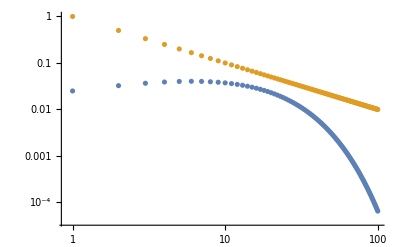

```mathematica
ListLogLogPlot[{xlist,ylist}]
```

```mathematica
Manipulate[ListLogLogPlot[{Table[NIntegrate[f[n,i]/. g-> 1 /.a -> 1,{x,-∞,1}],{n,1,N}],Table[1/n,{n,1,N}] } ],{N,3,40,1},{i,2,N,1}]
```

```mathematica
Manipulate[ListLogLogPlot[{Table[NIntegrate[g[n,i]/. g-> 1 /.a -> 1,{x,-∞,1}],{n,1,N}],Table[1/n,{n,1,N}] } ],{N,3,40,1},{i,2,N,1}]
```

NormalDistribution::posprm: Parameter ⅈ\ √2 at position 2 in NormalDistribution[0, ⅈ\ √2] is expected to be positive.

NIntegrate::inumr: The integrand ⅇ^-1/2\ (-1 + x)^2\ (1 - ⅇ^-4/3\ (1 - x))\ (1 - x)\ PDF[NormalDistribution[0, ⅈ\ √2], x]/√2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

NormalDistribution::posprm: Parameter ⅈ/√2 at position 2 in NormalDistribution[0, ⅈ/√2] is expected to be positive.

NIntegrate::inumr: The integrand ⅇ^-(-1 + x)^2\ (1 - ⅇ^-2/3\ (1 - x))\ (1 - x)\ PDF[NormalDistribution[0, ⅈ/√2], x]/√π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

NormalDistribution::posprm: Parameter 0 at position 2 in NormalDistribution[0, 0] is expected to be positive.

General::stop: Further output of NormalDistribution :: posprm will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand ⅇ^-1/2\ n\ (-1 + x)^2 - x^2/2\ (1 - 3\ Power[« 2 »])\ (1 - ⅇ^-2\ (1 - n/3)\ (1 - x))\ √n\ (1 - x)/2\ √1 - 3/n\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NormalDistribution::posprm: Parameter ⅈ\ √2 at position 2 in NormalDistribution[0, ⅈ\ √2] is expected to be positive.

NIntegrate::inumr: The integrand ⅇ^-1/2\ (-1 + x)^2\ (1 - ⅇ^-4/3\ (1 - x))\ (1 - x)\ PDF[NormalDistribution[0, ⅈ\ √2], x]/√2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

NormalDistribution::posprm: Parameter ⅈ/√2 at position 2 in NormalDistribution[0, ⅈ/√2] is expected to be positive.

NIntegrate::inumr: The integrand ⅇ^-(-1 + x)^2\ (1 - ⅇ^-2/3\ (1 - x))\ (1 - x)\ PDF[NormalDistribution[0, ⅈ/√2], x]/√π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

NormalDistribution::posprm: Parameter 0 at position 2 in NormalDistribution[0, 0] is expected to be positive.

General::stop: Further output of NormalDistribution :: posprm will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumr: The integrand ⅇ^-1/2\ n\ (-1 + x)^2 - x^2/2\ (1 - 3\ Power[« 2 »])\ (1 - ⅇ^-2\ (1 - n/3)\ (1 - x))\ √n\ (1 - x)/2\ √1 - 3/n\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NormalDistribution::posprm: Parameter ⅈ\ √7 at position 2 in NormalDistribution[0, ⅈ\ √7] is expected to be positive.

NIntegrate::inumr: The integrand ⅇ^-1/2\ (-1 + x)^2\ (1 - ⅇ^-7/4\ (1 - x))\ (1 - x)\ PDF[NormalDistribution[0, ⅈ\ √7], x]/√2\ π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

NormalDistribution::posprm: Parameter ⅈ\ √3 at position 2 in NormalDistribution[0, ⅈ\ √3] is expected to be positive.

NIntegrate::inumr: The integrand ⅇ^-(-1 + x)^2\ (1 - ⅇ^-3/2\ (1 - x))\ (1 - x)\ PDF[NormalDistribution[0, ⅈ\ √3], x]/√π has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

NormalDistribution::posprm: Parameter ⅈ\ √5/3 at position 2 in NormalDistribution[0, ⅈ\ √5/3] is expected to be positive.

General::stop: Further output of NormalDistribution :: posprm will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^-3/2\ (-1 + x)^2\ (1 - ⅇ^-5/4\ (1 - x))\ √3/2\ π\ (1 - x)\ PDF[NormalDistribution[0, ⅈ\ √5/3], x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 1.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.